```mathematica
(* A Monte Carlo simulation of gas breakdown between parallel plates *)
(* nc is the distance between plates, expressed as the number of collision lengths *)(* ni is the voltage, expressed as a multiple of the ionization voltage *)
(* reps is the number of electrons to toss *)
PaschenMcPlates[nc_,ni_,reps_]:=Module[{results},
(* results will be a simple list of the ion counts produced by each electron *)
results=Table[
Module[{x0,x1,nIons,weight},
nIons=0;
x0=0;
weight=1;
(* This while loop is the Monte Carlo simulation *)
While[(x1=x0+RandomVariate[ExponentialDistribution[1]])≤nc,
(* If the electron has travelled far enough to gain enough energy
to ionize the molecule, then count an ion. *)
If[ni/nc(x1-x0)>1,nIons+=weight;weight*=2];
x0=x1;
];
nIons (* appends this count to the list of results *)
],{reps}];
(* Return the mean and error on the mean. *)
Around[Mean[results],StandardDeviation[results]/Sqrt[reps]]
]
```

```mathematica
res100=Table[{ni,PaschenMcPlates[100,ni,1000]},{ni,120,170,5}]
```

{{120,1.210.1710^14},{125,4.11.110^14},{130,1.330.2110^15},{135,2.21.810^16},{140,7.31.110^15},{145,7.4.10^16},{150,5.81.210^16},{155,1.510.2810^17},{160,3.40.610^17},{165,1.80.510^18},{170,1.480.2610^18}}

```mathematica
ListPlot[res100]
```

-Graphics-

```mathematica
res=Table[{ni,PaschenMcPlates[100,ni,1000]},{ni,31,34,.2}]
```

{{31.,27.61.7},{31.2,32.02.7},{31.4,33.82.1},{31.6,37.4.},{31.8,37.22.6},{32.,41.63.2},{32.2,43.22.7},{32.4,50.4.},{32.6,54.5.},{32.8,60.6.},{33.,54.33.1},{33.2,61.4.},{33.4,63.4.},{33.6,74.4.},{33.8,78.6.},{34.,85.6.}}

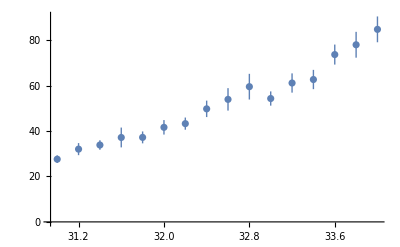

```mathematica
ListPlot[res]
```

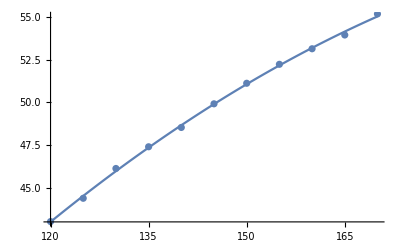

```mathematica
Show[p100,ListPlot[res100]]
```

```mathematica
model100["CovarianceMatrix"]
```

{{13.0006,-0.181658,0.000626992},{-0.181658,0.00254457,-8.80333×10^-6},{0.000626992,-8.80333×10^-6,3.05284×10^-8}}

```mathematica
NSolve[model100[x]==50,x]
```

{{x→145.396},{x→314.975}}

```mathematica
NewPoint[nc_,ni1_,ni2_,reps_]:=Module[{res,val,err,model,sol},
res=Table[{ni,PaschenMcPlates[nc,ni,reps]},{ni,ni1,ni2,(ni2-ni1)/15}];
val=Table[{a[[1]],a[[2]]["Value"]},{a,res}];
err=Table[a[[2]]["Uncertainty"],{a,res}];
model=LinearModelFit[val,{x,x^2},x,Weights->1/err^2];
sol=NSolve[model[x]==50,x];
Print[sol];
Show[Plot[model[x],{x,ni1,ni2}],ListPlot[res]]
]
```

{{x→27.2038},{x→32.4625}}

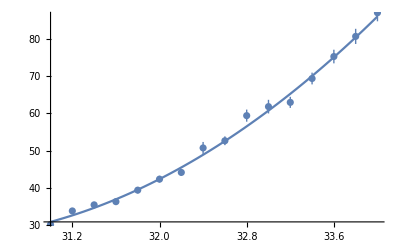

```mathematica
NewPoint[100,31,34,10000]
```

{{x→43.4859},{x→52.2177}}

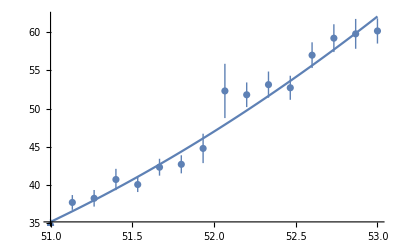

```mathematica
NewPoint[200,51,53,10000]
```

{{x→14.4062},{x→21.6292}}

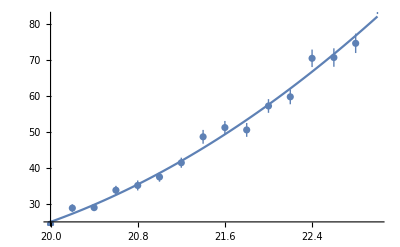

```mathematica
NewPoint[50,20,23,2000]
```

{{x→10.8212},{x→16.2745}}

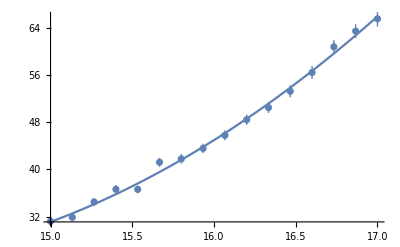

```mathematica
NewPoint[25,15,17,4000]
```

{{x→6.53834},{x→15.213}}

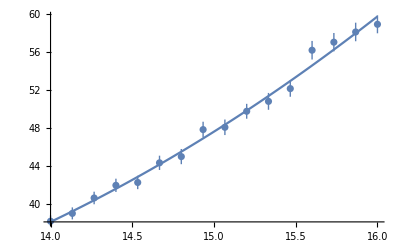

```mathematica
NewPoint[12.5,14,16,4000]
```

{{x→-18.1226},{x→24.448}}

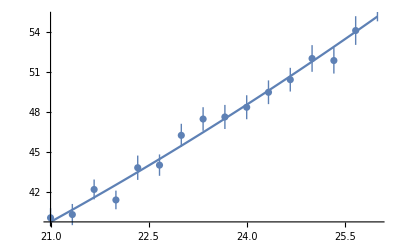

```mathematica
NewPoint[6.25,21,26,10000]
```

{{x→-157.531},{x→26.2056}}

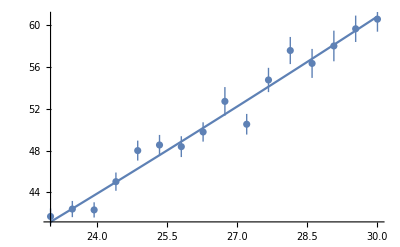

```mathematica
NewPoint[6,23,30,10000]
```

{{x→-18.8821},{x→28.4451}}

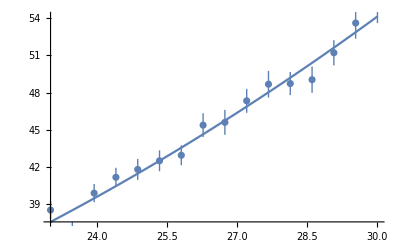

```mathematica
NewPoint[5.75,23,30,10000]
```

{{x→-23.7544},{x→31.3557}}

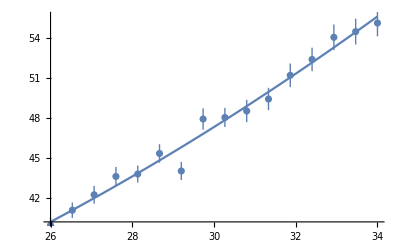

```mathematica
NewPoint[5.5,26,34,20000]
```

{{x→-50.3479},{x→35.6402}}

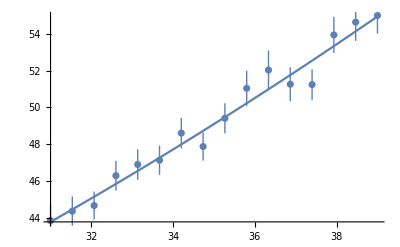

```mathematica
NewPoint[5.25,31,39,20000]
```

```mathematica
res120=Table[{ni,PaschenMcPlates[120,ni,1000]},{ni,120,170,5}]
```

{{120,43.970.11},{125,45.590.11},{130,47.500.11},{135,49.020.12},{140,50.570.12},{145,52.000.12},{150,53.550.12},{155,54.970.13},{160,56.130.13},{165,57.570.13},{170,58.970.13}}

```mathematica
val120=Table[{a[[1]],a[[2]]["Value"]},{a,res120}]
```

{{120,43.97},{125,45.587},{130,47.496},{135,49.016},{140,50.574},{145,51.995},{150,53.553},{155,54.973},{160,56.126},{165,57.566},{170,58.966}}

```mathematica
err120=Table[a[[2]]["Uncertainty"],{a,res120}]
```

{0.108429,0.110248,0.112448,0.115243,0.120453,0.120089,0.122353,0.125164,0.128236,0.12843,0.133299}

```mathematica
model120=LinearModelFit[val120,{x,x^2},x,Weights->1/err120^2]
```

FittedModel[-12.7976+0.597008 x-0.00103251 x^2]

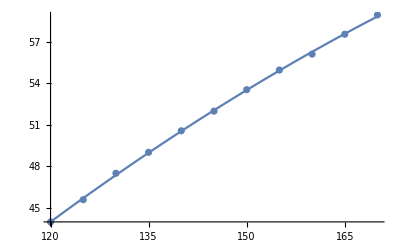

```mathematica
Show[Plot[model120[x],{x,120,170}],ListPlot[res120]]
```

```mathematica
NSolve[model120[x]==50,x]
```

{{x→138.236},{x→439.974}}

```mathematica
model100["Function"]
```

-14.4943+0.648336 #1-0.00140829 #1^2&

```mathematica
model100["BestFitParameters"]
```

{-14.4943,0.648336,-0.00140829}

```mathematica
Solve[a x^2+b x+c==50,x]
```

{{x→(-b-√(200 a+b^2-4 a c))/(2 a)},{x→(-b+√(200 a+b^2-4 a c))/(2 a)}}

```mathematica
f100=x/.%[[1]]
```

(-b-√(200 a+b^2-4 a c))/(2 a)

```mathematica
{D[f100,c],D[f100,b],D[f100,a]}
```

{1/(√(200 a+b^2-4 a c)),(-1-b/(√(200 a+b^2-4 a c)))/(2 a),-(200-4 c)/(4 a √(200 a+b^2-4 a c))-(-b-√(200 a+b^2-4 a c))/(2 a^2)}

```mathematica
res100a=Table[{ni,PaschenMcPlates[100,ni,1000]},{ni,10,300,10}]
```

{{10,0.00100.0010},{20,0.6650.025},{30,3.400.05},{40,8.050.07},{50,13.300.08},{60,18.610.08},{70,23.760.09},{80,28.300.09},{90,32.530.10},{100,36.410.10},{110,39.950.10},{120,42.950.11},{130,46.130.12},{140,48.650.13},{150,50.900.13},{160,53.000.13},{170,55.230.13},{180,57.040.14},{190,58.860.15},{200,60.040.16},{210,61.700.16},{220,63.190.16},{230,64.640.17},{240,65.560.17},{250,66.560.17},{260,67.820.18},{270,68.440.18},{280,69.280.19},{290,70.540.19},{300,71.280.20}}

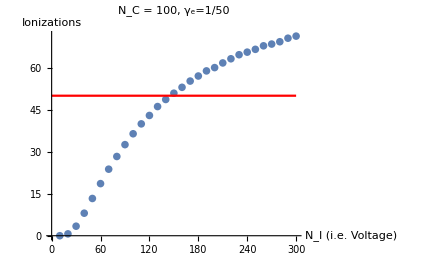

```mathematica
Show[ListPlot[res100a,PlotLabel->"N_C = 100, γ_e=1/50",AxesLabel->{"N_I (i.e. Voltage)","Ionizations"}],Plot[50,{x,0,300},PlotStyle->Red]]
```

```mathematica
all50={{55,585},{60,332},{70,211},{80,172},{100,146},{120,138},{140,137},{160,138},{180,141},{200,145},{280,163},{400,193},{560,232},{800,289},{1600,462},{3200,769}};
```

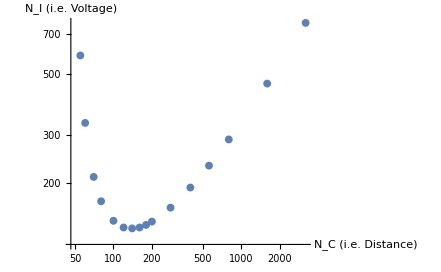

```mathematica
pp=ListLogLogPlot[all50,AxesLabel->{"N_C (i.e. Distance)","N_I (i.e. Voltage)"}]
```

```mathematica
new50={{5.5,31.36},{5.75,28.45},{6,26.21},{6.25,24.45},{12.5,15.21},{25,16.27},{50,21.63},{100,32.46},{200,52.22}};
```

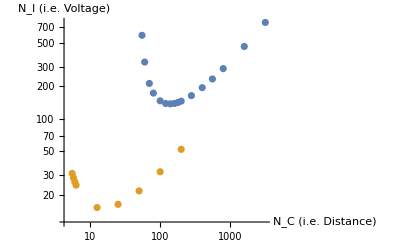

```mathematica
ListLogLogPlot[{all50,new50},AxesLabel->{"N_C (i.e. Distance)","N_I (i.e. Voltage)"}]
```

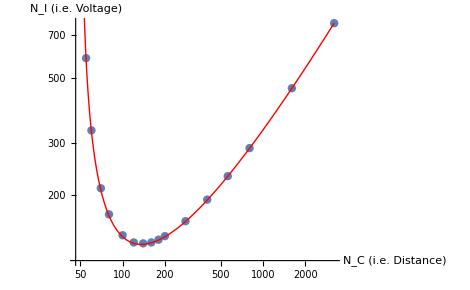

```mathematica
Show[pp,LogLogPlot[1 nc/Log[nc/50],{nc,50,3200},PlotStyle->{Red,Thin}]]
```

```mathematica
(* A Monte Carlo simulation of gas breakdown between parallel plates *)
(* nc is the distance between plates, expressed as the number of collision lengths *)(* ni is the voltage, expressed as a multiple of the ionization voltage *)
(* reps is the number of electrons to toss *)
PaschenMcSpheres[nc_,ni_,reps_]:=Module[{results},
(* results will be a simple list of the ion counts produced by each electron *)
results=Table[
Module[{x0,x1,nIons,ϕ},
ϕ[x_]:=(-5/4 ni)/(4 x/nc+1);
nIons=0;
x0=0;
(* This while loop is the Monte Carlo simulation *)
While[(x1=x0+RandomVariate[ExponentialDistribution[1]])≤nc,
(* If the electron has travelled far enough to gain enough energy
to ionize the molecule, then count an ion. *)
If[ϕ[x1]-ϕ[x0]>1,nIons++];
x0=x1;
];
nIons (* appends this count to the list of results *)
],{reps}];
(* Return the mean and error on the mean. *)
Around[Mean[results],StandardDeviation[results]/Sqrt[reps]]
]
```

```mathematica
(* A Monte Carlo simulation of gas breakdown between parallel plates *)
(* nc is the distance between plates, expressed as the number of collision lengths *)(* ni is the voltage, expressed as a multiple of the ionization voltage *)
(* reps is the number of electrons to toss *)
PaschenMcSpheresAlpha[nc_,ni_,reps_]:=Module[{results},
(* results will be a simple list of the ion counts produced by each electron *)
results=Table[
Module[{x0,x1,nIons,ϕ},
ϕ[x_]:=(-5/4 ni)/(4 x/nc+1);
nIons=0;
x0=0;
(* This while loop is the Monte Carlo simulation *)
While[(x1=x0+RandomVariate[ExponentialDistribution[1]])≤nc,
(* If the electron has travelled far enough to gain enough energy
to ionize the molecule, then count an ion. *)
If[ϕ[x1]-ϕ[x0]>1,Sow[4 x1/nc+1];nIons++];
x0=x1;
];
nIons (* appends this count to the list of results *)
],{reps}];
(* Return the mean and error on the mean. *)
Around[Mean[results],StandardDeviation[results]/Sqrt[reps]]
]
```

```mathematica
loc=Reap[PaschenMcSpheresAlpha[200,190,10000]]
```

{50.020.05,{{1.03748,1.05504,1.16237,1.18163,1.19669,1.2192,1.27387,1.28818,500173,2.80155,2.97752,3.13056,3.59438,3.94783,4.12942,4.98712}}}
 |  |  |  |

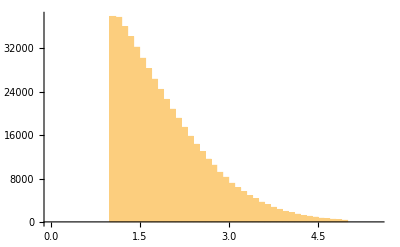

```mathematica
Histogram[loc[[2,1]],{0.1},PlotRange->{{0,5.5}, Automatic}]
```

```mathematica
loc1=Reap[PaschenMcSpheresAlpha[200,500,10000]]
```

{101.000.07,{{1.0155,1.0367,1.08266,1.09888,1.18626,1.1973,1.20166,1.21311,1010005,4.30607,4.38581,4.46089,4.50754,4.60987,4.71863,4.89991}}}
 |  |  |  |

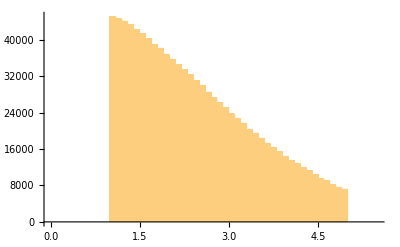

```mathematica
Histogram[loc1[[2,1]],{0.1},PlotRange->{{0,5.5}, Automatic}]
```

```mathematica
loc2=Reap[PaschenMcSpheresAlpha[200,80,10000]]
```

{20.0900.027,{{1.01059,1.03488,1.08574,1.1116,1.14329,1.15824,1.18644,200885,1.70676,1.79184,1.89786,2.0212,2.06884,2.1636,2.40023}}}
 |  |  |  |

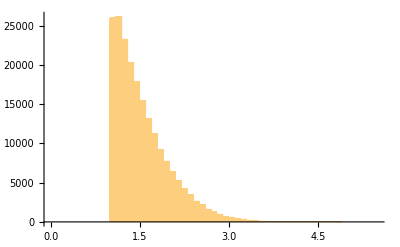

```mathematica
Histogram[loc2[[2,1]],{0.1},PlotRange->{{0,5.5}, Automatic}]
```

```mathematica
PaschenMcSpheres[100,300,100]
```

55.20.5

```mathematica
(* Records starts of paths *)
PaschenMcSpheresX[nc_,ni_,reps_]:=Module[{results},
(* results will be a simple list of the ion counts produced by each electron *)
results=Table[
Module[{x0,x1,nIons,ϕ},
ϕ[x_]:=(-5/4 ni)/(4 x/nc+1);
nIons=0;
x0=0;
(* This while loop is the Monte Carlo simulation *)
While[(x1=x0+RandomVariate[ExponentialDistribution[1]])≤nc,
Sow[4 x0/nc+1];
(* If the electron has travelled far enough to gain enough energy
to ionize the molecule, then count an ion. *)
If[ϕ[x1]-ϕ[x0]>1,nIons++];
x0=x1;
];
nIons (* appends this count to the list of results *)
],{reps}];
(* Return the mean and error on the mean. *)
Around[Mean[results],StandardDeviation[results]/Sqrt[reps]]
]
```

```mathematica
locX=Reap[PaschenMcSpheresX[200,190,10000]]
```

{50.110.05,{{1,1.01892,1.0411,1.06618,1.09661,1.09959,1.16126,1.17666,1.21119,1.23177,1.25443,1.25537,1.25541,1.26819,1.31945,1.32045,1.32837,1.338,1999751,4.56866,4.60261,4.66726,4.68058,4.70597,4.70696,4.71705,4.74088,4.74816,4.74844,4.7593,4.76334,4.79212,4.81595,4.88328,4.89663,4.92001,4.94363}}}
 |  |  |  |

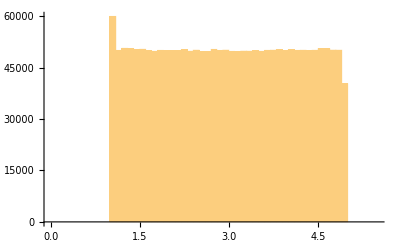

```mathematica
Histogram[locX[[2,1]],{0.1},PlotRange->{{0,5.5}, Automatic}]
```

```mathematica
NewPointSpheres[nc_,ni1_,ni2_,step_,reps_]:=Module[{res,val,err,model,sol},
res=Table[{ni,PaschenMcSpheres[nc,ni,reps]},{ni,ni1,ni2,step}];
val=Table[{a[[1]],a[[2]]["Value"]},{a,res}];
err=Table[a[[2]]["Uncertainty"],{a,res}];
model=LinearModelFit[val,{x,x^2},x,Weights->1/err^2];
sol=NSolve[model[x]==50,x];
Print[sol];
Show[Plot[model[x],{x,ni1,ni2}],ListPlot[res]]
]
```

{{x→233.449},{x→561.431}}

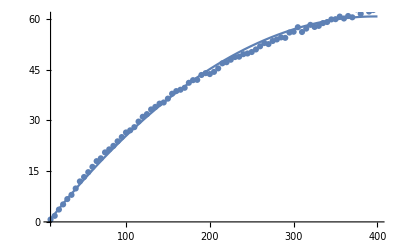

```mathematica
NewPointSpheres[100,10,400,100]
```

{{x→244.056},{x→585.328}}

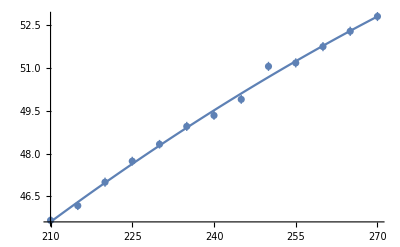

```mathematica
NewPointSpheres[100,210,270,1000]
```

```mathematica
allSphere={{55,1153},{60,652},{70,394},{80,310},{100,244},{120,218}};
```

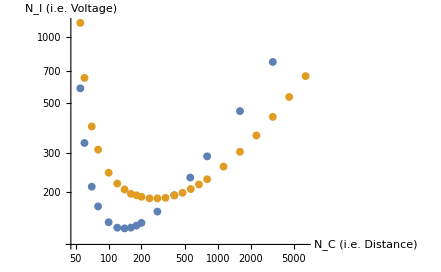

```mathematica
pps=ListLogLogPlot[{all50,allSphere},AxesLabel->{"N_C (i.e. Distance)","N_I (i.e. Voltage)"}]
```

{{x→1153.22},{x→1873.01}}

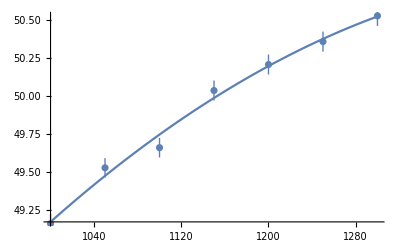

```mathematica
NewPointSpheres[55,1000,1300,50,10000]
```

{{x→1169.79},{x→2760.89}}

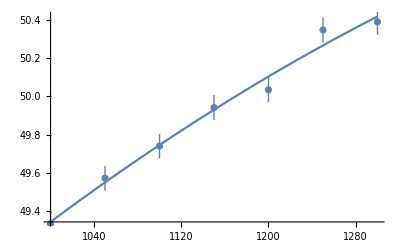

```mathematica
NewPointSpheres[55,1000,1300,50,10000]
```

{{x→1168.25},{x→2468.54}}

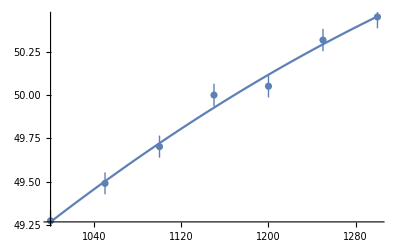

```mathematica
NewPointSpheres[55,1000,1300,50,10000]
```

{{x→652.081},{x→1636.12}}

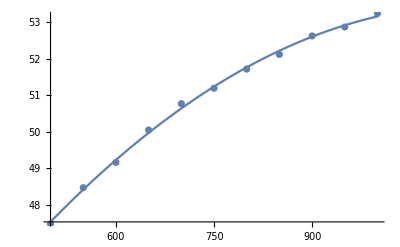

```mathematica
NewPointSpheres[60,500,1000,50,10000]
```

{{x→394.004},{x→990.597}}

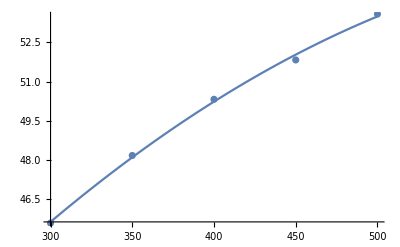

```mathematica
NewPointSpheres[70,300,500,50,4000]
```

{{x→310.309},{x→798.067}}

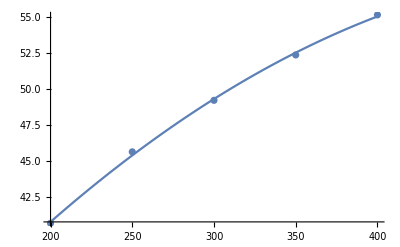

```mathematica
NewPointSpheres[80,200,400,50,2000]
```

{{x→217.897},{x→666.69}}

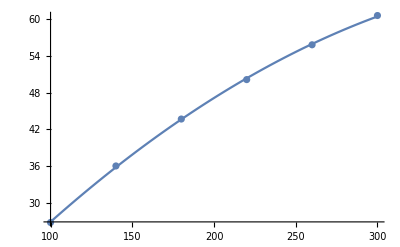

```mathematica
NewPointSpheres[120,100,300,40,1000]
```

{{x→205.163},{x→750.862}}

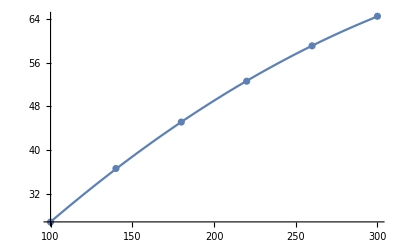

```mathematica
NewPointSpheres[140,100,300,40,1000]
```

```mathematica
AppendTo[allSphere,{6400,664}]
```

{{55,1153},{60,652},{70,394},{80,310},{100,244},{120,218},{140,205},{160,196},{180,193},{200,190},{237,187},{280,187},{332,188},{400,193},{476,198},{566,206},{673,216},{800,228},{1131,260},{1600,303},{2263,359},{3200,435},{4525,535},{6400,664}}

{{x→40.2621},{x→664.053}}

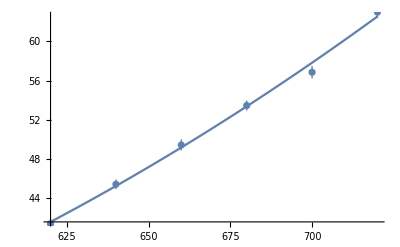

```mathematica
NewPointSpheres[6400,620,720,20,100]
```

```mathematica
n=Nc/4 Integrate[Exp[-Nc/(5 Ni)x^2],{x,1,5}]/.{Nc->x,Ni->y}
```

1/8 √(5 π) √x √y (-Erf[(√x)/(√5 √y)]+Erf[(√5 √x)/(√y)])

```mathematica
FindRoot[(n/.x->200)==50,{y,100}]
```

{y→191.033}

```mathematica
sol1=Table[x=55 Exp[t];{x,y/.FindRoot[n==50,{y,100}][[1]]},{t,0,5,0.1}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{55.,1165.97},{60.7844,613.381},{67.1772,436.777},{74.2422,350.843},{82.0504,300.671},{90.6797,268.248},{100.217,245.92},{110.756,229.885},{122.405,218.043},{135.278,209.146},{149.506,202.407},{165.229,197.317},{182.606,193.534},{201.811,190.828},{223.036,189.043},{246.493,188.074},{272.417,187.851},{301.067,188.33},{332.731,189.481},{367.724,191.289},{406.398,193.748},{449.139,196.857},{496.376,200.621},{548.58,205.053},{606.275,210.168},{670.037,215.986},{740.506,222.535},{818.385,229.843},{904.456,237.947},{999.578,246.886},{1104.7,256.708},{1220.89,267.464},{1349.29,279.211},{1491.2,292.013},{1648.03,305.941},{1821.35,321.073},{2012.9,337.493},{2224.6,355.297},{2458.57,374.586},{2717.13,395.472},{3002.9,418.079},{3318.72,442.539},{3667.75,468.999},{4053.49,497.618},{4479.8,528.568},{4950.94,562.039},{5471.64,598.236},{6047.09,637.384},{6683.07,679.725},{7385.94,725.526},{8162.72,775.075}}

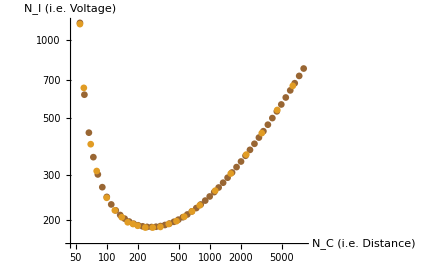

```mathematica
ListLogLogPlot[{sol1,allSphere},PlotStyle->{Brown,RGBColor[0.880722,0.611041,0.142051]},
AxesLabel->{"N_C (i.e. Distance)","N_I (i.e. Voltage)"}]
```

```mathematica
ListPlot[Table[{i},{i,10}]]//FullForm
```

Graphics[List[List[],List[List[List[Directive[PointSize[0.0128333],RGBColor[0.368417,0.506779,0.709798],AbsoluteThickness[1.6]],Point[List[List[1.,1.],List[1.,1.]]]],List[Directive[PointSize[0.0128333],RGBColor[0.880722,0.611041,0.142051],AbsoluteThickness[1.6]],Point[List[List[1.,2.],List[1.,2.]]]],List[Directive[PointSize[0.0128333],RGBColor[0.560181,0.691569,0.194885],AbsoluteThickness[1.6]],Point[List[List[1.,3.],List[1.,3.]]]],List[Directive[PointSize[0.0128333],RGBColor[0.922526,0.385626,0.209179],AbsoluteThickness[1.6]],Point[List[List[1.,4.],List[1.,4.]]]],List[Directive[PointSize[0.0128333],RGBColor[0.528488,0.470624,0.701351],AbsoluteThickness[1.6]],Point[List[List[1.,5.],List[1.,5.]]]],List[Directive[PointSize[0.0128333],RGBColor[0.772079,0.431554,0.102387],AbsoluteThickness[1.6]],Point[List[List[1.,6.],List[1.,6.]]]],List[Directive[PointSize[0.0128333],RGBColor[0.363898,0.618501,0.782349],AbsoluteThickness[1.6]],Point[List[List[1.,7.],List[1.,7.]]]],List[Directive[PointSize[0.0128333],RGBColor[1,0.75,0],AbsoluteThickness[1.6]],Point[List[List[1.,8.],List[1.,8.]]]],List[Directive[PointSize[0.0128333],RGBColor[0.647624,0.37816,0.614037],AbsoluteThickness[1.6]],Point[List[List[1.,9.],List[1.,9.]]]],List[Directive[PointSize[0.0128333],RGBColor[0.571589,0.586483,0.],AbsoluteThickness[1.6]],Point[List[List[1.,10.],List[1.,10.]]]]]],List[List[],List[]]],List[Rule[DisplayFunction,Identity],Rule[DisplayFunction,Identity],Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,List[True,True]],Rule[AxesLabel,List[None,None]],Rule[AxesOrigin,List[0.,0]],RuleDelayed[DisplayFunction,Identity],Rule[Frame,List[List[False,False],List[False,False]]],Rule[FrameLabel,List[List[None,None],List[None,None]]],Rule[FrameTicks,List[List[Automatic,Automatic],List[Automatic,Automatic]]],Rule[GridLines,List[None,None]],Rule[GridLinesStyle,Directive[GrayLevel[0.5,0.4]]],Rule[Method,List[Rule["OptimizePlotMarkers",True],Rule["OptimizePlotMarkers",True],Rule["CoordinatesToolOptions",List[Rule["DisplayFunction",Function[List[Identity[Part[Slot[1],1]],Identity[Part[Slot[1],2]]]]],Rule["CopiedValueFunction",Function[List[Identity[Part[Slot[1],1]],Identity[Part[Slot[1],2]]]]]]]]],Rule[PlotRange,List[List[0.,1.],List[0,10.]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[List[Scaled[0.02],Scaled[0.02]],List[Scaled[0.02],Scaled[0.05]]]],Rule[Ticks,List[Automatic,Automatic]]]]